# Ecological Models

## Predator - Prey system

```mathematica
(*Dynamical system for a prey(x)-predator(y) system*)
de1:=x'=a*x-b*x*y
de2:=y'=-c*y+d*x*y
```

```mathematica
(*Define the differential equations in terms of their variables*)
Prey[a_,b_]=de1;
Predator[c_,d_]=de2;
```

```mathematica
(*Plot the prey-predator dynamical system*)
(*Assumed a, b, c, d > 0*)
(*In this system, there is no assumption on the Prey's food source -> assumed unlimited*)
Manipulate[StreamPlot[{Prey[a,b],Predator[c,d]},{x,0,10},{y,0,10},FrameLabel->{"Prey","Predator"}],{a,0,10,Appearance->"Open"},{b,0,10,Appearance->"Open"},{c,0,10,Appearance->"Open"},{d,0,10,Appearance->"Open"}]
```

## Application to Cosmology

```mathematica
(*Define the dynamical system for coupled dark matter (z) and dark energy (x)*)
dex:=x'=-3*x*(1+wx)-q*x*z
dez:=z'=-3*z + q*x*z
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{dex==0,dez==0},{x,z}]
```

{{x→0,z→0},{x→3/q,z→-(3 (1+wx))/q}}

```mathematica
FP[1]={x/.FPs[[1,1]],z/.FPs[[1,2]]};
FP[2]={x/.FPs[[2,1]],z/.FPs[[2,2]]};
```

```mathematica
(*Put fixed points into a table*)
FPs=Table[FP[i],{i,1,2}];
```

```mathematica
(*Find the 4D Jacobian matrix for general system of equations. D[] differentiates each expression*)
J=Simplify[{{D[dex,x],D[dex,z]}, {D[dez,x],D[dez,z]}}];
J//MatrixForm
```

(-3-3 wx-q z | -q x
q z | -3+q x)

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point*)
FPTable=Table[{FPs[[i]]//MatrixForm,Simplify[J/.{x->FPs[[i,1]],z->FPs[[i,2]]}]//MatrixForm,Eigenvalues[J/.{x->FPs[[i,1]],z->FPs[[i,2]]}]//MatrixForm,Eigenvectors[J/.{x->FPs[[i,1]],z->FPs[[i,2]]}]//MatrixForm},{i,1,2}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix and eigenvalues*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(0
0) | (-3 (1+wx) | 0
0 | -3) | (-3
3 (-1-wx)) | (0 | 1
1 | 0)
(3/q
-(3 (1+wx))/q) | (0 | -3
-3 (1+wx) | 0) | (-3 √(1+wx)
3 √(1+wx)) | (1/(√(1+wx)) | 1
-1/(√(1+wx)) | 1)

```mathematica
(*Define the differential equations in terms of their variables*)
DE[wx_,q_]=dex;
DM[q_]=dez;
```

```mathematica
Manipulate[StreamPlot[{DE[wx,q],DM[q]},{x,0,1},{z,0,1},FrameLabel->{"x","z"}],{q,0,20,Appearance->"Open"},{wx,-2,2,Appearance->"Open"}]
```

## Modified Energy Density System

### Non-Compact x - z Phase Space

```mathematica
(*Define the dynamical system for coupled dark matter (z) and dark energy (x)*)
dex:=x'=-3*x*(1+wx+ϵ*x)-q*x*z
dez:=z'=-3*z + q*x*z
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{dex==0,dez==0},{x,z}]
```

{{x→3/q,z→-(3 (q+q wx+3 ϵ))/q^2},{x→0,z→0},{x→-(1+wx)/ϵ,z→0}}

```mathematica
FP[1]={x/.FPs[[1,1]],z/.FPs[[1,2]]};
FP[2]={x/.FPs[[2,1]],z/.FPs[[2,2]]};
FP[3]={x/.FPs[[3,1]],z/.FPs[[3,2]]};
```

```mathematica
(*Put fixed points into a table*)
FPs=Table[FP[i],{i,1,3}];
```

```mathematica
(*Find the 4D Jacobian matrix for general system of equations. D[] differentiates each expression*)
J=Simplify[{{D[dex,x],D[dex,z]}, {D[dez,x],D[dez,z]}}];
J//MatrixForm
```

(-3-3 wx-q z-6 x ϵ | -q x
q z | -3+q x)

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point*)
FPTable=Table[{FPs[[i]]//MatrixForm,Simplify[J/.{x->FPs[[i,1]],z->FPs[[i,2]]}]//MatrixForm,Eigenvalues[J/.{x->FPs[[i,1]],z->FPs[[i,2]]}]//MatrixForm,Eigenvectors[J/.{x->FPs[[i,1]],z->FPs[[i,2]]}]//MatrixForm},{i,1,3}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix and eigenvalues*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(3/q
-(3 (q+q wx+3 ϵ))/q^2) | (-(9 ϵ)/q | -3
-(3 (q+q wx+3 ϵ))/q | 0) | ((3 (-3 q ϵ-q √(4 q^2+4 q^2 wx+12 q ϵ+9 ϵ^2)))/(2 q^2)
(3 (-3 q ϵ+q √(4 q^2+4 q^2 wx+12 q ϵ+9 ϵ^2)))/(2 q^2)) | (-(-3 ϵ-√(4 q^2+4 q^2 wx+12 q ϵ+9 ϵ^2))/(2 (q+q wx+3 ϵ)) | 1
-(-3 ϵ+√(4 q^2+4 q^2 wx+12 q ϵ+9 ϵ^2))/(2 (q+q wx+3 ϵ)) | 1)
(0
0) | (-3 (1+wx) | 0
0 | -3) | (-3
3 (-1-wx)) | (0 | 1
1 | 0)
(-(1+wx)/ϵ
0) | (3 (1+wx) | (q (1+wx))/ϵ
0 | -3-(q (1+wx))/ϵ) | (3 (1+wx)
-(q+q wx+3 ϵ)/ϵ) | (1 | 0
-(q (1+wx))/(q+q wx+6 ϵ+3 wx ϵ) | 1)

```mathematica
(*Find condition for first fixed point to be complex*)
wxCond=Solve[4 q^2+4 q^2 wx+12 q ϵ+9 ϵ^2==0,{q,ϵ,wx}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{wx→-(2 q+3 ϵ)^2/(4 q^2)},{q→0,ϵ→0}}

```mathematica
wxCondition=wx/.wxCond[[1]]
```

-(2 q+3 ϵ)^2/(4 q^2)

```mathematica
(*Maximum value wx can be for the first fixed point to be complex for positive values of ϵ and q -> Fig. 9a*)
(*For this wx the two eigenvalues are the same*)
wxMax1=wxCondition/.{ϵ->0.01,q->.1}
```

-1.3225

```mathematica
(*Maximum value wx can be for the first fixed point to be complex for positive q and negative ϵ -> Fig. 9b*)
(*For this wx the two eigenvalues are the same*)
wxMax2=wxCondition/.{ϵ->-0.25,q->1}
```

-0.390625

```mathematica
(*Define the differential equations in terms of their variables*)
DE[wx_,q_,ϵ_]=dex;
DM[q_]=dez;
```

```mathematica
Manipulate[StreamPlot[{DE[wx,q,ϵ],DM[q]},{x,0,5},{z,0,3},FrameLabel->{"x","z"}],{q,0,20,Appearance->"Open"},{wx,-10,10,Appearance->"Open"},{ϵ,-2,2,Appearance->"Open"}]
```

### Non-Compact x - y - z Phase Space

```mathematica
(*Define the dynamical system for coupled dark matter (z) and dark energy (x)*)
de1:=x'=-3*y*x*(1+wx+ϵ*x)-q*x*y*z
de2:=y'=-y^2-(1/6)*(x+z+3*wx*x+3*ϵ*x^2)
de3:=z'=-3*y*z + q*x*y*z
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{de1==0,de2==0,de3==0},{x,y,z}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{y→0,z→-x-3 wx x-3 x^2 ϵ},{x→0,y→0,z→0},{x→3/q,y→-(√(-q wx-3 ϵ))/q,z→-(3 (q+q wx+3 ϵ))/q^2},{x→3/q,y→(√(-q wx-3 ϵ))/q,z→-(3 (q+q wx+3 ϵ))/q^2},{x→(-1-wx)/ϵ,y→-(√(-1-wx))/(√3 √ϵ),z→0},{x→(-1-wx)/ϵ,y→(√(-1-wx))/(√3 √ϵ),z→0}}

```mathematica
(*Remove arrows from fixed points and put them into a common variable name*)
FP[1]={x,y/.FPs[[1,1]],z/.FPs[[1,2]]};
FP[2]={x/.FPs[[2,1]],y/.FPs[[2,2]],z/.FPs[[2,3]]};
FP[3]={x/.FPs[[3,1]],y/.FPs[[3,2]],z/.FPs[[3,3]]};
FP[4]={x/.FPs[[4,1]],y/.FPs[[4,2]],z/.FPs[[4,3]]};
FP[5]={x/.FPs[[5,1]],y/.FPs[[5,2]],z/.FPs[[5,3]]};
FP[6]={x/.FPs[[6,1]],y/.FPs[[6,2]],z/.FPs[[6,3]]};
```

```mathematica
(*Put fixed points into a table*)
FPs=Table[FP[i],{i,1,6}];
```

```mathematica
(*Find the 4D Jacobian matrix for general system of equations. D[] differentiates each expression*)
J=Simplify[{{D[de1,x],D[de1,y],D[de1,z]}, {D[de2,x],D[de2,y],D[de2,z]},{D[de3,x],D[de3,y],D[de3,z]}}];
J//MatrixForm
```

(-y (3+3 wx+q z+6 x ϵ) | -x (3+3 wx+q z+3 x ϵ) | -q x y
1/6 (-1-3 wx-6 x ϵ) | -2 y | -1/6
q y z | (-3+q x) z | (-3+q x) y)

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point*)
FPTable=Table[{FPs[[i]]//MatrixForm,Simplify[J/.{x->FPs[[i,1]],y->FPs[[i,2]],z->FPs[[i,3]]}]//MatrixForm,Eigenvalues[J/.{x->FPs[[i,1]],y->FPs[[i,2]],z->FPs[[i,3]]}]//MatrixForm,Eigenvectors[J/.{x->FPs[[i,1]],y->FPs[[i,2]],z->FPs[[i,3]]}]//MatrixForm},{i,1,6}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix and eigenvalues*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(x
0
-x-3 wx x-3 x^2 ϵ) | (0 | x (3 wx (-1+q x)-3 (1+x ϵ)+q x (1+3 x ϵ)) | 0
1/6 (-1-3 wx-6 x ϵ) | 0 | -1/6
0 | -x (-3+q x) (1+3 wx+3 x ϵ) | 0) | (0
-(ⅈ √x √(-wx-3 wx^2+q wx x+3 q wx^2 x-4 x ϵ-9 wx x ϵ+2 q x^2 ϵ+9 q wx x^2 ϵ-6 x^2 ϵ^2+6 q x^3 ϵ^2))/(√2)
(ⅈ √x √(-wx-3 wx^2+q wx x+3 q wx^2 x-4 x ϵ-9 wx x ϵ+2 q x^2 ϵ+9 q wx x^2 ϵ-6 x^2 ϵ^2+6 q x^3 ϵ^2))/(√2)) | (-1/(1+3 wx+6 x ϵ) | 0 | 1
-(-3-3 wx+q x+3 q wx x-3 x ϵ+3 q x^2 ϵ)/((-3+q x) (1+3 wx+3 x ϵ)) | (ⅈ √(-wx-3 wx^2+q wx x+3 q wx^2 x-4 x ϵ-9 wx x ϵ+2 q x^2 ϵ+9 q wx x^2 ϵ-6 x^2 ϵ^2+6 q x^3 ϵ^2))/(√2 √x (-3+q x) (1+3 wx+3 x ϵ)) | 1
-(-3-3 wx+q x+3 q wx x-3 x ϵ+3 q x^2 ϵ)/((-3+q x) (1+3 wx+3 x ϵ)) | -(ⅈ √(-wx-3 wx^2+q wx x+3 q wx^2 x-4 x ϵ-9 wx x ϵ+2 q x^2 ϵ+9 q wx x^2 ϵ-6 x^2 ϵ^2+6 q x^3 ϵ^2))/(√2 √x (-3+q x) (1+3 wx+3 x ϵ)) | 1)
(0
0
0) | (0 | 0 | 0
1/6 (-1-3 wx) | 0 | -1/6
0 | 0 | 0) | (0
0
0) | (-1/(1+3 wx) | 0 | 1
0 | 1 | 0
0 | 0 | 0)
(3/q
-(√(-q wx-3 ϵ))/q
-(3 (q+q wx+3 ϵ))/q^2) | ((9 √(-q wx-3 ϵ) ϵ)/q^2 | 0 | (3 √(-q wx-3 ϵ))/q
-(q+3 q wx+18 ϵ)/(6 q) | (2 √(-q wx-3 ϵ))/q | -1/6
(3 √(-q wx-3 ϵ) (q+q wx+3 ϵ))/q^2 | 0 | 0) | ((2 √(-q wx-3 ϵ))/q
(3 (3 √(-q wx-3 ϵ) ϵ-√(-4 q^3 wx-4 q^3 wx^2-12 q^2 ϵ-24 q^2 wx ϵ-36 q ϵ^2-9 q wx ϵ^2-27 ϵ^3)))/(2 q^2)
(3 (3 √(-q wx-3 ϵ) ϵ+√(-4 q^3 wx-4 q^3 wx^2-12 q^2 ϵ-24 q^2 wx ϵ-36 q ϵ^2-9 q wx ϵ^2-27 ϵ^3)))/(2 q^2)) | (0 | 1 | 0
(4 q^2 wx+12 q ϵ-9 q wx ϵ-27 ϵ^2-3 √(-q wx-3 ϵ) √(-4 q^3 wx-4 q^3 wx^2-12 q^2 ϵ-24 q^2 wx ϵ-36 q ϵ^2-9 q wx ϵ^2-27 ϵ^3))/(2 (-3 q^2 wx-3 q^2 wx^2-9 q ϵ-21 q wx ϵ-36 ϵ^2+√(-q wx-3 ϵ) √(-4 q^3 wx-4 q^3 wx^2-12 q^2 ϵ-24 q^2 wx ϵ-36 q ϵ^2-9 q wx ϵ^2-27 ϵ^3))) | (q (-2 q √(-q wx-3 ϵ)-6 q wx √(-q wx-3 ϵ)-33 √(-q wx-3 ϵ) ϵ+√(-4 q^3 wx-4 q^3 wx^2-12 q^2 ϵ-24 q^2 wx ϵ-36 q ϵ^2-9 q wx ϵ^2-27 ϵ^3)))/(12 (-3 q^2 wx-3 q^2 wx^2-9 q ϵ-21 q wx ϵ-36 ϵ^2+√(-q wx-3 ϵ) √(-4 q^3 wx-4 q^3 wx^2-12 q^2 ϵ-24 q^2 wx ϵ-36 q ϵ^2-9 q wx ϵ^2-27 ϵ^3))) | 1
-(4 q^2 wx+12 q ϵ-9 q wx ϵ-27 ϵ^2+3 √(-q wx-3 ϵ) √(-4 q^3 wx-4 q^3 wx^2-12 q^2 ϵ-24 q^2 wx ϵ-36 q ϵ^2-9 q wx ϵ^2-27 ϵ^3))/(2 (3 q^2 wx+3 q^2 wx^2+9 q ϵ+21 q wx ϵ+36 ϵ^2+√(-q wx-3 ϵ) √(-4 q^3 wx-4 q^3 wx^2-12 q^2 ϵ-24 q^2 wx ϵ-36 q ϵ^2-9 q wx ϵ^2-27 ϵ^3))) | (q (2 q √(-q wx-3 ϵ)+6 q wx √(-q wx-3 ϵ)+33 √(-q wx-3 ϵ) ϵ+√(-4 q^3 wx-4 q^3 wx^2-12 q^2 ϵ-24 q^2 wx ϵ-36 q ϵ^2-9 q wx ϵ^2-27 ϵ^3)))/(12 (3 q^2 wx+3 q^2 wx^2+9 q ϵ+21 q wx ϵ+36 ϵ^2+√(-q wx-3 ϵ) √(-4 q^3 wx-4 q^3 wx^2-12 q^2 ϵ-24 q^2 wx ϵ-36 q ϵ^2-9 q wx ϵ^2-27 ϵ^3))) | 1)
(3/q
(√(-q wx-3 ϵ))/q
-(3 (q+q wx+3 ϵ))/q^2) | (-(9 √(-q wx-3 ϵ) ϵ)/q^2 | 0 | -(3 √(-q wx-3 ϵ))/q
-(q+3 q wx+18 ϵ)/(6 q) | -(2 √(-q wx-3 ϵ))/q | -1/6
-(3 √(-q wx-3 ϵ) (q+q wx+3 ϵ))/q^2 | 0 | 0) | (-(2 √(-q wx-3 ϵ))/q
(3 (-3 √(-q wx-3 ϵ) ϵ-√(-4 q^3 wx-4 q^3 wx^2-12 q^2 ϵ-24 q^2 wx ϵ-36 q ϵ^2-9 q wx ϵ^2-27 ϵ^3)))/(2 q^2)
(3 (-3 √(-q wx-3 ϵ) ϵ+√(-4 q^3 wx-4 q^3 wx^2-12 q^2 ϵ-24 q^2 wx ϵ-36 q ϵ^2-9 q wx ϵ^2-27 ϵ^3)))/(2 q^2)) | (0 | 1 | 0
(4 q^2 wx+12 q ϵ-9 q wx ϵ-27 ϵ^2-3 √(-q wx-3 ϵ) √(-4 q^3 wx-4 q^3 wx^2-12 q^2 ϵ-24 q^2 wx ϵ-36 q ϵ^2-9 q wx ϵ^2-27 ϵ^3))/(2 (-3 q^2 wx-3 q^2 wx^2-9 q ϵ-21 q wx ϵ-36 ϵ^2+√(-q wx-3 ϵ) √(-4 q^3 wx-4 q^3 wx^2-12 q^2 ϵ-24 q^2 wx ϵ-36 q ϵ^2-9 q wx ϵ^2-27 ϵ^3))) | -(q (-2 q √(-q wx-3 ϵ)-6 q wx √(-q wx-3 ϵ)-33 √(-q wx-3 ϵ) ϵ+√(-4 q^3 wx-4 q^3 wx^2-12 q^2 ϵ-24 q^2 wx ϵ-36 q ϵ^2-9 q wx ϵ^2-27 ϵ^3)))/(12 (-3 q^2 wx-3 q^2 wx^2-9 q ϵ-21 q wx ϵ-36 ϵ^2+√(-q wx-3 ϵ) √(-4 q^3 wx-4 q^3 wx^2-12 q^2 ϵ-24 q^2 wx ϵ-36 q ϵ^2-9 q wx ϵ^2-27 ϵ^3))) | 1
-(4 q^2 wx+12 q ϵ-9 q wx ϵ-27 ϵ^2+3 √(-q wx-3 ϵ) √(-4 q^3 wx-4 q^3 wx^2-12 q^2 ϵ-24 q^2 wx ϵ-36 q ϵ^2-9 q wx ϵ^2-27 ϵ^3))/(2 (3 q^2 wx+3 q^2 wx^2+9 q ϵ+21 q wx ϵ+36 ϵ^2+√(-q wx-3 ϵ) √(-4 q^3 wx-4 q^3 wx^2-12 q^2 ϵ-24 q^2 wx ϵ-36 q ϵ^2-9 q wx ϵ^2-27 ϵ^3))) | -(q (2 q √(-q wx-3 ϵ)+6 q wx √(-q wx-3 ϵ)+33 √(-q wx-3 ϵ) ϵ+√(-4 q^3 wx-4 q^3 wx^2-12 q^2 ϵ-24 q^2 wx ϵ-36 q ϵ^2-9 q wx ϵ^2-27 ϵ^3)))/(12 (3 q^2 wx+3 q^2 wx^2+9 q ϵ+21 q wx ϵ+36 ϵ^2+√(-q wx-3 ϵ) √(-4 q^3 wx-4 q^3 wx^2-12 q^2 ϵ-24 q^2 wx ϵ-36 q ϵ^2-9 q wx ϵ^2-27 ϵ^3))) | 1)
((-1-wx)/ϵ
-(√(-1-wx))/(√3 √ϵ)
0) | ((√3 (-1-wx)^(3/2))/(√ϵ) | 0 | (q (-1-wx)^(3/2))/(√3 ϵ^(3/2))
1/6 (5+3 wx) | (2 √(-1-wx))/(√3 √ϵ) | -1/6
0 | 0 | (√(-1-wx) (q+q wx+3 ϵ))/(√3 ϵ^(3/2))) | ((2 √(-1-wx))/(√3 √ϵ)
-(√3 √(-1-wx) (1+wx))/(√ϵ)
(√(-1-wx) (q+q wx+3 ϵ))/(√3 ϵ^(3/2))) | (0 | 1 | 0
-(2 √3 √(-1-wx))/(√ϵ) | 1 | 0
-(q+q wx)/(q+q wx+6 ϵ+3 wx ϵ) | -(√3 (2 ϵ^(3/2)+wx ϵ^(3/2)))/(2 √(-1-wx) (q+q wx+6 ϵ+3 wx ϵ)) | 1)
((-1-wx)/ϵ
(√(-1-wx))/(√3 √ϵ)
0) | (-(√3 (-1-wx)^(3/2))/(√ϵ) | 0 | -(q (-1-wx)^(3/2))/(√3 ϵ^(3/2))
1/6 (5+3 wx) | -(2 √(-1-wx))/(√3 √ϵ) | -1/6
0 | 0 | -(√(-1-wx) (q+q wx+3 ϵ))/(√3 ϵ^(3/2))) | (-(2 √(-1-wx))/(√3 √ϵ)
(√3 √(-1-wx) (1+wx))/(√ϵ)
-(√(-1-wx) (q+q wx+3 ϵ))/(√3 ϵ^(3/2))) | (0 | 1 | 0
(2 √3 √(-1-wx))/(√ϵ) | 1 | 0
-(q+q wx)/(q+q wx+6 ϵ+3 wx ϵ) | (√3 (2 ϵ^(3/2)+wx ϵ^(3/2)))/(2 √(-1-wx) (q+q wx+6 ϵ+3 wx ϵ)) | 1)

```mathematica
Eq1[q_,wx_,ϵ_]=de1;
Eq2[wx_,ϵ_]=de2;
Eq3[q_]=de3;
```

```mathematica
Manipulate[StreamPlot3D[{Eq1[q,wx,ϵ],Eq2[wx,ϵ],Eq3[q]},{x,0,15},{y,-5,5},{z,0,10},AxesLabel->{"x","y","z"}],{q,0,1,Appearance->"Open"},{wx,-5,1,Appearance->"Open"},{ϵ,-1,1,Appearance->"Open"}]
```

### x - y Numeric Phase Space

#### Fig 9 a

```mathematica
(*Clear all variables*)
ClearAll["Global`*"];
```

```mathematica
(*Define the dynamical system for coupled dark matter (z) and dark energy (x)*)
de1t:=x1'[t]==-3*y1[t]*x1[t]*(1+wx+ϵ*x1[t])-q*x1[t]*y1[t]*z1[t]
de2t:=y1'[t]==-y1[t]^2-(1/6)*(x1[t]+z1[t]+3*wx*x1[t]+3*ϵ*x1[t]^2)
de3t:=z1'[t]==-3*y1[t]*z1[t]+ q*x1[t]*y1[t]*z1[t]
```

```mathematica
q=1;
wx=-2;
ϵ=0.1;
```

```mathematica
traj[x0_,y0_,z0_]=NDSolve[{de1t,de2t,de3t, x1[0]==x0,y1[0]==y0,z1[0]==z0}, {x1,y1,z1},{t,-50,50}];
```

NDSolve::ndinnt: Initial condition x0 is not a number or a rectangular array of numbers.

```mathematica
sol[1]=traj[0.02,0.01,0.009];
sol[2]=traj[0.02,0.05,0.009];
sol[3]=traj[0.8,0.055,0.009];
sol[4]=traj[0.99,0.06,0.009];
sol[5]=traj[2.991,1,0.009];
sol[6]=traj[0.02,0.09,0.009];
```

NDSolve::ndsz: At t == -5.83121, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == -11.916, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {-49.998} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

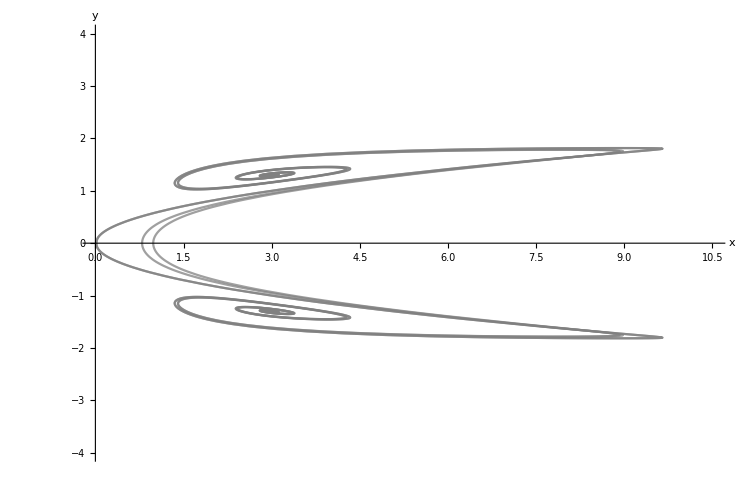

```mathematica
ParametricPlot[Evaluate[Table[{x1[t],y1[t]}/.sol[i],{i,1,6}], {t,-50,50},PlotStyle -> {{Gray, Opacity[0.75]}},PlotRange->{{0,10.5},{-4,4}}],AxesLabel->{"x","y"}]
```

InterpolatingFunction::dmval: Input value {-49.998} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

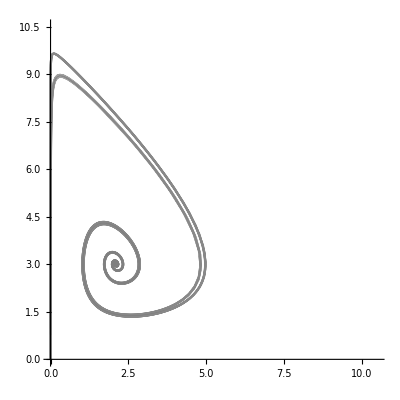

```mathematica
ParametricPlot[Evaluate[Table[{z1[t],x1[t]}/.sol[i],{i,1,6}], {t,-50,50},PlotStyle -> {{Gray, Opacity[0.75]}},PlotRange->{{0,10.5},{0,10.5}}]]
```

#### Fig 9 b

```mathematica
(*Clear all variables*)
ClearAll["Global`*"];
```

```mathematica
(*Define the dynamical system for coupled dark matter (z) and dark energy (x)*)
de1:=x'=-3*y*x*(1+wx+ϵ*x)-q*x*y*z
de2:=y'=-y^2-(1/6)*(x+z+3*wx*x+3*ϵ*x^2)
de3:=z'=-3*y*z + q*x*y*z
```

```mathematica
q=1;
wx=-0.5;
ϵ=-0.25;
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{de1==0,de2==0,de3==0},{x,y,z}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

{{y→0.,z→0.25 x (2.+3. x)},{x→0.,y→0.,z→0.},{x→2.,y→-0.816497,z→0.},{x→2.,y→0.816497,z→0.},{x→3.,y→-1.11803,z→0.75},{x→3.,y→1.11803,z→0.75}}

```mathematica
(*Remove arrows from fixed points and put them into a common variable name*)
FP[1]={x,y/.FPs[[1,1]],z/.FPs[[1,2]]};
FP[2]={x/.FPs[[2,1]],y/.FPs[[2,2]],z/.FPs[[2,3]]};
FP[3]={x/.FPs[[3,1]],y/.FPs[[3,2]],z/.FPs[[3,3]]};
FP[4]={x/.FPs[[4,1]],y/.FPs[[4,2]],z/.FPs[[4,3]]};
FP[5]={x/.FPs[[5,1]],y/.FPs[[5,2]],z/.FPs[[5,3]]};
FP[6]={x/.FPs[[6,1]],y/.FPs[[6,2]],z/.FPs[[6,3]]};
```

```mathematica
(*Put fixed points into a table*)
FPs=Table[FP[i],{i,1,6}];
```

```mathematica
(*Find the 4D Jacobian matrix for general system of equations. D[] differentiates each expression*)
J=Simplify[{{D[de1,x],D[de1,y],D[de1,z]}, {D[de2,x],D[de2,y],D[de2,z]},{D[de3,x],D[de3,y],D[de3,z]}}];
J//MatrixForm
```

(y (-1.5+1.5 x-1. z) | x (-1.5+0.75 x-z) | -x y
0.0833333+0.25 x | -2 y | -1/6
y z | (-3+x) z | (-3+x) y)

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point*)
FPTable=Table[{FPs[[i]]//MatrixForm,Simplify[J/.{x->FPs[[i,1]],y->FPs[[i,2]],z->FPs[[i,3]]}]//MatrixForm,Eigenvalues[J/.{x->FPs[[i,1]],y->FPs[[i,2]],z->FPs[[i,3]]}]//MatrixForm,Eigenvectors[J/.{x->FPs[[i,1]],y->FPs[[i,2]],z->FPs[[i,3]]}]//MatrixForm},{i,1,6}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix and eigenvalues*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(x
0
-x-3 wx x-3 x^2 ϵ) | (0 | x (3 wx (-1+q x)-3 (1+x ϵ)+q x (1+3 x ϵ)) | 0
1/6 (-1-3 wx-6 x ϵ) | 0 | -1/6
0 | -x (-3+q x) (1+3 wx+3 x ϵ) | 0) | (0
-(ⅈ √x √(-wx-3 wx^2+q wx x+3 q wx^2 x-4 x ϵ-9 wx x ϵ+2 q x^2 ϵ+9 q wx x^2 ϵ-6 x^2 ϵ^2+6 q x^3 ϵ^2))/(√2)
(ⅈ √x √(-wx-3 wx^2+q wx x+3 q wx^2 x-4 x ϵ-9 wx x ϵ+2 q x^2 ϵ+9 q wx x^2 ϵ-6 x^2 ϵ^2+6 q x^3 ϵ^2))/(√2)) | (-1/(1+3 wx+6 x ϵ) | 0 | 1
-(-3-3 wx+q x+3 q wx x-3 x ϵ+3 q x^2 ϵ)/((-3+q x) (1+3 wx+3 x ϵ)) | (ⅈ √(-wx-3 wx^2+q wx x+3 q wx^2 x-4 x ϵ-9 wx x ϵ+2 q x^2 ϵ+9 q wx x^2 ϵ-6 x^2 ϵ^2+6 q x^3 ϵ^2))/(√2 √x (-3+q x) (1+3 wx+3 x ϵ)) | 1
-(-3-3 wx+q x+3 q wx x-3 x ϵ+3 q x^2 ϵ)/((-3+q x) (1+3 wx+3 x ϵ)) | -(ⅈ √(-wx-3 wx^2+q wx x+3 q wx^2 x-4 x ϵ-9 wx x ϵ+2 q x^2 ϵ+9 q wx x^2 ϵ-6 x^2 ϵ^2+6 q x^3 ϵ^2))/(√2 √x (-3+q x) (1+3 wx+3 x ϵ)) | 1)
(0
0
0) | (0 | 0 | 0
1/6 (-1-3 wx) | 0 | -1/6
0 | 0 | 0) | (0
0
0) | (-1/(1+3 wx) | 0 | 1
0 | 1 | 0
0 | 0 | 0)
(3/q
-(√(-q wx-3 ϵ))/q
-(3 (q+q wx+3 ϵ))/q^2) | ((9 √(-q wx-3 ϵ) ϵ)/q^2 | 0 | (3 √(-q wx-3 ϵ))/q
-(q+3 q wx+18 ϵ)/(6 q) | (2 √(-q wx-3 ϵ))/q | -1/6
(3 √(-q wx-3 ϵ) (q+q wx+3 ϵ))/q^2 | 0 | 0) | ((2 √(-q wx-3 ϵ))/q
(3 (3 √(-q wx-3 ϵ) ϵ-√(-4 q^3 wx-4 q^3 wx^2-12 q^2 ϵ-24 q^2 wx ϵ-36 q ϵ^2-9 q wx ϵ^2-27 ϵ^3)))/(2 q^2)
(3 (3 √(-q wx-3 ϵ) ϵ+√(-4 q^3 wx-4 q^3 wx^2-12 q^2 ϵ-24 q^2 wx ϵ-36 q ϵ^2-9 q wx ϵ^2-27 ϵ^3)))/(2 q^2)) | (0 | 1 | 0
(4 q^2 wx+12 q ϵ-9 q wx ϵ-27 ϵ^2-3 √(-q wx-3 ϵ) √(-4 q^3 wx-4 q^3 wx^2-12 q^2 ϵ-24 q^2 wx ϵ-36 q ϵ^2-9 q wx ϵ^2-27 ϵ^3))/(2 (-3 q^2 wx-3 q^2 wx^2-9 q ϵ-21 q wx ϵ-36 ϵ^2+√(-q wx-3 ϵ) √(-4 q^3 wx-4 q^3 wx^2-12 q^2 ϵ-24 q^2 wx ϵ-36 q ϵ^2-9 q wx ϵ^2-27 ϵ^3))) | (q (-2 q √(-q wx-3 ϵ)-6 q wx √(-q wx-3 ϵ)-33 √(-q wx-3 ϵ) ϵ+√(-4 q^3 wx-4 q^3 wx^2-12 q^2 ϵ-24 q^2 wx ϵ-36 q ϵ^2-9 q wx ϵ^2-27 ϵ^3)))/(12 (-3 q^2 wx-3 q^2 wx^2-9 q ϵ-21 q wx ϵ-36 ϵ^2+√(-q wx-3 ϵ) √(-4 q^3 wx-4 q^3 wx^2-12 q^2 ϵ-24 q^2 wx ϵ-36 q ϵ^2-9 q wx ϵ^2-27 ϵ^3))) | 1
-(4 q^2 wx+12 q ϵ-9 q wx ϵ-27 ϵ^2+3 √(-q wx-3 ϵ) √(-4 q^3 wx-4 q^3 wx^2-12 q^2 ϵ-24 q^2 wx ϵ-36 q ϵ^2-9 q wx ϵ^2-27 ϵ^3))/(2 (3 q^2 wx+3 q^2 wx^2+9 q ϵ+21 q wx ϵ+36 ϵ^2+√(-q wx-3 ϵ) √(-4 q^3 wx-4 q^3 wx^2-12 q^2 ϵ-24 q^2 wx ϵ-36 q ϵ^2-9 q wx ϵ^2-27 ϵ^3))) | (q (2 q √(-q wx-3 ϵ)+6 q wx √(-q wx-3 ϵ)+33 √(-q wx-3 ϵ) ϵ+√(-4 q^3 wx-4 q^3 wx^2-12 q^2 ϵ-24 q^2 wx ϵ-36 q ϵ^2-9 q wx ϵ^2-27 ϵ^3)))/(12 (3 q^2 wx+3 q^2 wx^2+9 q ϵ+21 q wx ϵ+36 ϵ^2+√(-q wx-3 ϵ) √(-4 q^3 wx-4 q^3 wx^2-12 q^2 ϵ-24 q^2 wx ϵ-36 q ϵ^2-9 q wx ϵ^2-27 ϵ^3))) | 1)
(3/q
(√(-q wx-3 ϵ))/q
-(3 (q+q wx+3 ϵ))/q^2) | (-(9 √(-q wx-3 ϵ) ϵ)/q^2 | 0 | -(3 √(-q wx-3 ϵ))/q
-(q+3 q wx+18 ϵ)/(6 q) | -(2 √(-q wx-3 ϵ))/q | -1/6
-(3 √(-q wx-3 ϵ) (q+q wx+3 ϵ))/q^2 | 0 | 0) | (-(2 √(-q wx-3 ϵ))/q
(3 (-3 √(-q wx-3 ϵ) ϵ-√(-4 q^3 wx-4 q^3 wx^2-12 q^2 ϵ-24 q^2 wx ϵ-36 q ϵ^2-9 q wx ϵ^2-27 ϵ^3)))/(2 q^2)
(3 (-3 √(-q wx-3 ϵ) ϵ+√(-4 q^3 wx-4 q^3 wx^2-12 q^2 ϵ-24 q^2 wx ϵ-36 q ϵ^2-9 q wx ϵ^2-27 ϵ^3)))/(2 q^2)) | (0 | 1 | 0
(4 q^2 wx+12 q ϵ-9 q wx ϵ-27 ϵ^2-3 √(-q wx-3 ϵ) √(-4 q^3 wx-4 q^3 wx^2-12 q^2 ϵ-24 q^2 wx ϵ-36 q ϵ^2-9 q wx ϵ^2-27 ϵ^3))/(2 (-3 q^2 wx-3 q^2 wx^2-9 q ϵ-21 q wx ϵ-36 ϵ^2+√(-q wx-3 ϵ) √(-4 q^3 wx-4 q^3 wx^2-12 q^2 ϵ-24 q^2 wx ϵ-36 q ϵ^2-9 q wx ϵ^2-27 ϵ^3))) | -(q (-2 q √(-q wx-3 ϵ)-6 q wx √(-q wx-3 ϵ)-33 √(-q wx-3 ϵ) ϵ+√(-4 q^3 wx-4 q^3 wx^2-12 q^2 ϵ-24 q^2 wx ϵ-36 q ϵ^2-9 q wx ϵ^2-27 ϵ^3)))/(12 (-3 q^2 wx-3 q^2 wx^2-9 q ϵ-21 q wx ϵ-36 ϵ^2+√(-q wx-3 ϵ) √(-4 q^3 wx-4 q^3 wx^2-12 q^2 ϵ-24 q^2 wx ϵ-36 q ϵ^2-9 q wx ϵ^2-27 ϵ^3))) | 1
-(4 q^2 wx+12 q ϵ-9 q wx ϵ-27 ϵ^2+3 √(-q wx-3 ϵ) √(-4 q^3 wx-4 q^3 wx^2-12 q^2 ϵ-24 q^2 wx ϵ-36 q ϵ^2-9 q wx ϵ^2-27 ϵ^3))/(2 (3 q^2 wx+3 q^2 wx^2+9 q ϵ+21 q wx ϵ+36 ϵ^2+√(-q wx-3 ϵ) √(-4 q^3 wx-4 q^3 wx^2-12 q^2 ϵ-24 q^2 wx ϵ-36 q ϵ^2-9 q wx ϵ^2-27 ϵ^3))) | -(q (2 q √(-q wx-3 ϵ)+6 q wx √(-q wx-3 ϵ)+33 √(-q wx-3 ϵ) ϵ+√(-4 q^3 wx-4 q^3 wx^2-12 q^2 ϵ-24 q^2 wx ϵ-36 q ϵ^2-9 q wx ϵ^2-27 ϵ^3)))/(12 (3 q^2 wx+3 q^2 wx^2+9 q ϵ+21 q wx ϵ+36 ϵ^2+√(-q wx-3 ϵ) √(-4 q^3 wx-4 q^3 wx^2-12 q^2 ϵ-24 q^2 wx ϵ-36 q ϵ^2-9 q wx ϵ^2-27 ϵ^3))) | 1)
((-1-wx)/ϵ
-(√(-1-wx))/(√3 √ϵ)
0) | ((√3 (-1-wx)^(3/2))/(√ϵ) | 0 | (q (-1-wx)^(3/2))/(√3 ϵ^(3/2))
1/6 (5+3 wx) | (2 √(-1-wx))/(√3 √ϵ) | -1/6
0 | 0 | (√(-1-wx) (q+q wx+3 ϵ))/(√3 ϵ^(3/2))) | ((2 √(-1-wx))/(√3 √ϵ)
-(√3 √(-1-wx) (1+wx))/(√ϵ)
(√(-1-wx) (q+q wx+3 ϵ))/(√3 ϵ^(3/2))) | (0 | 1 | 0
-(2 √3 √(-1-wx))/(√ϵ) | 1 | 0
-(q+q wx)/(q+q wx+6 ϵ+3 wx ϵ) | -(√3 (2 ϵ^(3/2)+wx ϵ^(3/2)))/(2 √(-1-wx) (q+q wx+6 ϵ+3 wx ϵ)) | 1)
((-1-wx)/ϵ
(√(-1-wx))/(√3 √ϵ)
0) | (-(√3 (-1-wx)^(3/2))/(√ϵ) | 0 | -(q (-1-wx)^(3/2))/(√3 ϵ^(3/2))
1/6 (5+3 wx) | -(2 √(-1-wx))/(√3 √ϵ) | -1/6
0 | 0 | -(√(-1-wx) (q+q wx+3 ϵ))/(√3 ϵ^(3/2))) | (-(2 √(-1-wx))/(√3 √ϵ)
(√3 √(-1-wx) (1+wx))/(√ϵ)
-(√(-1-wx) (q+q wx+3 ϵ))/(√3 ϵ^(3/2))) | (0 | 1 | 0
(2 √3 √(-1-wx))/(√ϵ) | 1 | 0
-(q+q wx)/(q+q wx+6 ϵ+3 wx ϵ) | (√3 (2 ϵ^(3/2)+wx ϵ^(3/2)))/(2 √(-1-wx) (q+q wx+6 ϵ+3 wx ϵ)) | 1)

```mathematica
(*Define the dynamical system for coupled dark matter (z) and dark energy (x)*)
de1t:=x1'[t]==-3*y1[t]*x1[t]*(1+wx+ϵ*x1[t])-q*x1[t]*y1[t]*z1[t]
de2t:=y1'[t]==-y1[t]^2-(1/6)*(x1[t]+z1[t]+3*wx*x1[t]+3*ϵ*x1[t]^2)
de3t:=z1'[t]==-3*y1[t]*z1[t]+ q*x1[t]*y1[t]*z1[t]
```

```mathematica
q=1;
wx=-0.5;
ϵ=-0.25;
```

```mathematica
(*Analyse the unstable spiral fixed point*)
(*z and y values at the spiral point for this case*)
zSpiral=-(3 (q+q wx+3 ϵ))/q^2
ySpiralPlus=(√(-q wx-3 ϵ))/q
ySpiralMinus=-(√(-q wx-3 ϵ))/q
```

0.75

```mathematica
(*Find the eigenvalues when taking the negative root for y value at spiral fixed point*)
Eig1=(2 √(-q wx-3 ϵ))/q
```

2.23607

```mathematica
Eig2=(3 (3 √(-q wx-3 ϵ) ϵ-√(-4 q^3 wx-4 q^3 wx^2-12 q^2 ϵ-24 q^2 wx ϵ-36 q ϵ^2-9 q wx ϵ^2-27 ϵ^3)))/(2 q^2)
```

-1.25779-1.10926 ⅈ

```mathematica
(Eig3=3 (3 √(-q wx-3 ϵ) ϵ+√(-4 q^3 wx-4 q^3 wx^2-12 q^2 ϵ-24 q^2 wx ϵ-36 q ϵ^2-9 q wx ϵ^2-27 ϵ^3)))/(2 q^2)
```

-1.25779+1.10926 ⅈ

```mathematica
(*Find the eigenvalues when taking the positive root for y value at spiral fixed point*)
Eig4=-(2 √(-q wx-3 ϵ))/q
```

-2.23607

```mathematica
Eig5=(3 (-3 √(-q wx-3 ϵ) ϵ-√(-4 q^3 wx-4 q^3 wx^2-12 q^2 ϵ-24 q^2 wx ϵ-36 q ϵ^2-9 q wx ϵ^2-27 ϵ^3)))/(2 q^2)
```

1.25779-1.10926 ⅈ

```mathematica
Eig6=(3 (-3 √(-q wx-3 ϵ) ϵ+√(-4 q^3 wx-4 q^3 wx^2-12 q^2 ϵ-24 q^2 wx ϵ-36 q ϵ^2-9 q wx ϵ^2-27 ϵ^3)))/(2 q^2)
```

1.25779+1.10926 ⅈ

```mathematica
traj[x0_,y0_,z0_]=NDSolve[{de1t,de2t,de3t, x1[0]==x0,y1[0]==y0,z1[0]==z0}, {x1,y1,z1},{t,-50,50}];
```

NDSolve::ndinnt: Initial condition x0 is not a number or a rectangular array of numbers.

```mathematica
sol[1]=traj[2,0.1,0.009];
sol[2]=traj[0.5,0.1,0.009];
sol[3]=traj[5,0.1,0.009];
sol[4]=traj[4,0.1,0.009];
sol[5]=traj[1,0.1,0.009];
sol[6]=traj[3,2,0.009];
sol[7]=traj[4,3,0.009];
sol[8]=traj[1,2.5,0.009];
```

NDSolve::ndsz: At t == -0.553018, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == -0.353627, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == -0.406503, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {-49.998} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dprec: The precision of input value {-49.998} and/or the interpolation grid is insufficient to compute the value.

InterpolatingFunction::dprec: The precision of input value {-47.9571} and/or the interpolation grid is insufficient to compute the value.

General::stop: Further output of InterpolatingFunction::dprec will be suppressed during this calculation.

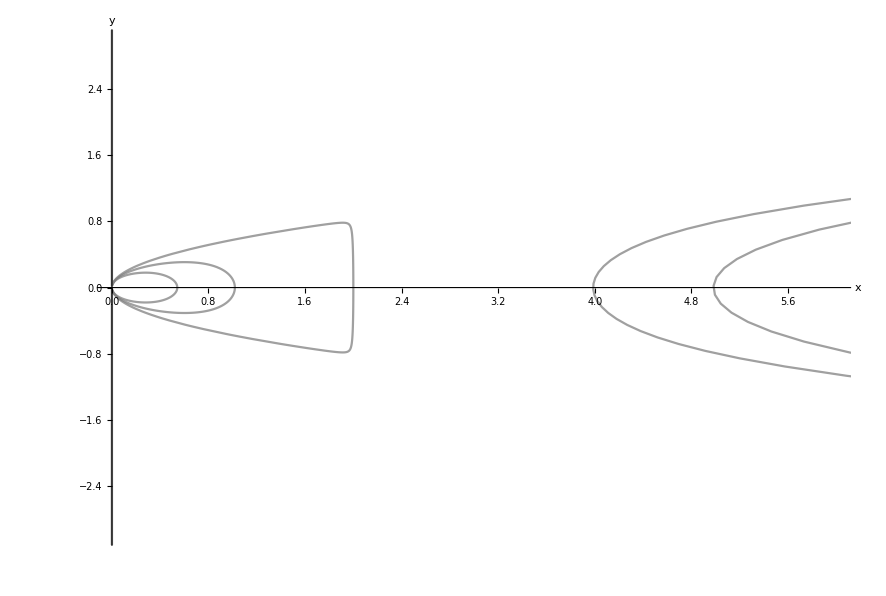

```mathematica
ParametricPlot[Evaluate[Table[{x1[t],y1[t]}/.sol[i],{i,1,8}], {t,-50,50},PlotStyle -> {{Gray, Opacity[0.75]}},PlotRange->{{0,6},{-3,3}}],AxesLabel->{"x","y"}]
```

### Compactification

### Compact x - z Phase Space

```mathematica
(*Define the dynamical system for coupled dark matter (z) and dark energy (x)*)
deX:=X'=-3*X*(1-X)*(1+wx+ϵ*(X/(1-X)))-q*X*(1-X)*Z/(1-Z)
deZ:=Z'=-3*Z*(1-Z) + q*(X/(1-X))*Z*(1-Z)
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{deX==0,deZ==0},{X,Z}]Fig 9 b
```

{{X→3/(3+q),Z→-(3 (q+q wx+3 ϵ))/(-3 q+q^2-3 q wx-9 ϵ)},{X→0,Z→0},{X→(1+wx)/(1+wx-ϵ),Z→0}}

```mathematica
FP[1]={X/.FPs[[1,1]],Z/.FPs[[1,2]]};
FP[2]={X/.FPs[[2,1]],Z/.FPs[[2,2]]};
FP[3]={X/.FPs[[3,1]],Z/.FPs[[3,2]]};
```

```mathematica
(*Put fixed points into a table*)
FPs=Table[FP[i],{i,1,3}];
```

```mathematica
(*Find the 4D Jacobian matrix for general system of equations. D[] differentiates each expression*)
J=Simplify[{{D[deX,X],D[deX,Z]}, {D[deZ,X],D[deZ,Z]}}];
J//MatrixForm
```

((3+3 wx (-1+2 X) (-1+Z)-3 Z+q Z-2 X (3-3 ϵ+Z (-3+q+3 ϵ)))/(-1+Z) | (q (-1+X) X)/(-1+Z)^2
-(q (-1+Z) Z)/(-1+X)^2 | ((-3+(3+q) X) (-1+2 Z))/(-1+X))

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point*)
FPTable=Table[{FPs[[i]]//MatrixForm,Simplify[J/.{X->FPs[[i,1]],Z->FPs[[i,2]]}]//MatrixForm,Eigenvalues[J/.{X->FPs[[i,1]],Z->FPs[[i,2]]}]//MatrixForm,Eigenvectors[J/.{X->FPs[[i,1]],Z->FPs[[i,2]]}]//MatrixForm},{i,1,3}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix and eigenvalues*)
(*Extra fixed points from compactification at {X = 1, Z = 0},{X = 1, Z = 1},{X = 0, Z = 1}*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(3/(3+q)
-(3 (q+q wx+3 ϵ))/(-3 q+q^2-3 q wx-9 ϵ)) | (-(9 ϵ)/q | -(3 (q^2-3 q (1+wx)-9 ϵ)^2)/(q^2 (3+q)^2)
-(3 q (3+q)^2 (q+q wx+3 ϵ))/((q^2-3 q (1+wx)-9 ϵ)^2) | 0) | ((3 (-243 q^3 ϵ+54 q^5 ϵ-3 q^7 ϵ-486 q^3 wx ϵ-162 q^4 wx ϵ+54 q^5 wx ϵ+18 q^6 wx ϵ-243 q^3 wx^2 ϵ-162 q^4 wx^2 ϵ-27 q^5 wx^2 ϵ-1458 q^2 ϵ^2-486 q^3 ϵ^2+162 q^4 ϵ^2+54 q^5 ϵ^2-1458 q^2 wx ϵ^2-972 q^3 wx ϵ^2-162 q^4 wx ϵ^2-2187 q ϵ^3-1458 q^2 ϵ^3-243 q^3 ϵ^3-q (3+q)^2 (-3 q+q^2-3 q wx-9 ϵ)^2 √(4 q^2+4 q^2 wx+12 q ϵ+9 ϵ^2)))/(2 q^2 (3+q)^2 (-3 q+q^2-3 q wx-9 ϵ)^2)
(3 (-243 q^3 ϵ+54 q^5 ϵ-3 q^7 ϵ-486 q^3 wx ϵ-162 q^4 wx ϵ+54 q^5 wx ϵ+18 q^6 wx ϵ-243 q^3 wx^2 ϵ-162 q^4 wx^2 ϵ-27 q^5 wx^2 ϵ-1458 q^2 ϵ^2-486 q^3 ϵ^2+162 q^4 ϵ^2+54 q^5 ϵ^2-1458 q^2 wx ϵ^2-972 q^3 wx ϵ^2-162 q^4 wx ϵ^2-2187 q ϵ^3-1458 q^2 ϵ^3-243 q^3 ϵ^3+q (3+q)^2 (-3 q+q^2-3 q wx-9 ϵ)^2 √(4 q^2+4 q^2 wx+12 q ϵ+9 ϵ^2)))/(2 q^2 (3+q)^2 (-3 q+q^2-3 q wx-9 ϵ)^2)) | (-(-27 q^2 ϵ+18 q^3 ϵ-3 q^4 ϵ-54 q^2 wx ϵ+18 q^3 wx ϵ-27 q^2 wx^2 ϵ-162 q ϵ^2+54 q^2 ϵ^2-162 q wx ϵ^2-243 ϵ^3-9 q^2 √(4 q^2+4 q^2 wx+12 q ϵ+9 ϵ^2)+6 q^3 √(4 q^2+4 q^2 wx+12 q ϵ+9 ϵ^2)-q^4 √(4 q^2+4 q^2 wx+12 q ϵ+9 ϵ^2)-18 q^2 wx √(4 q^2+4 q^2 wx+12 q ϵ+9 ϵ^2)+6 q^3 wx √(4 q^2+4 q^2 wx+12 q ϵ+9 ϵ^2)-9 q^2 wx^2 √(4 q^2+4 q^2 wx+12 q ϵ+9 ϵ^2)-54 q ϵ √(4 q^2+4 q^2 wx+12 q ϵ+9 ϵ^2)+18 q^2 ϵ √(4 q^2+4 q^2 wx+12 q ϵ+9 ϵ^2)-54 q wx ϵ √(4 q^2+4 q^2 wx+12 q ϵ+9 ϵ^2)-81 ϵ^2 √(4 q^2+4 q^2 wx+12 q ϵ+9 ϵ^2))/(2 (3 q+q^2)^2 (q+q wx+3 ϵ)) | 1
-(-27 q^2 ϵ+18 q^3 ϵ-3 q^4 ϵ-54 q^2 wx ϵ+18 q^3 wx ϵ-27 q^2 wx^2 ϵ-162 q ϵ^2+54 q^2 ϵ^2-162 q wx ϵ^2-243 ϵ^3+9 q^2 √(4 q^2+4 q^2 wx+12 q ϵ+9 ϵ^2)-6 q^3 √(4 q^2+4 q^2 wx+12 q ϵ+9 ϵ^2)+q^4 √(4 q^2+4 q^2 wx+12 q ϵ+9 ϵ^2)+18 q^2 wx √(4 q^2+4 q^2 wx+12 q ϵ+9 ϵ^2)-6 q^3 wx √(4 q^2+4 q^2 wx+12 q ϵ+9 ϵ^2)+9 q^2 wx^2 √(4 q^2+4 q^2 wx+12 q ϵ+9 ϵ^2)+54 q ϵ √(4 q^2+4 q^2 wx+12 q ϵ+9 ϵ^2)-18 q^2 ϵ √(4 q^2+4 q^2 wx+12 q ϵ+9 ϵ^2)+54 q wx ϵ √(4 q^2+4 q^2 wx+12 q ϵ+9 ϵ^2)+81 ϵ^2 √(4 q^2+4 q^2 wx+12 q ϵ+9 ϵ^2))/(2 (3 q+q^2)^2 (q+q wx+3 ϵ)) | 1)
(0
0) | (-3 (1+wx) | 0
0 | -3) | (-3
3 (-1-wx)) | (0 | 1
1 | 0)
((1+wx)/(1+wx-ϵ)
0) | (3 (1+wx) | (q (1+wx) ϵ)/(1+wx-ϵ)^2
0 | -3-(q (1+wx))/ϵ) | (3 (1+wx)
-(q+q wx+3 ϵ)/ϵ) | (1 | 0
-(q (1+wx) ϵ^2)/((1+wx-ϵ)^2 (q+q wx+6 ϵ+3 wx ϵ)) | 1)

```mathematica
(*Find condition for first fixed point to be complex*)
wxCond=Solve[4 q^2+4 q^2 wx+12 q ϵ+9 ϵ^2==0,{q,ϵ,wx}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{wx→-(2 q+3 ϵ)^2/(4 q^2)},{q→0,ϵ→0}}

```mathematica
wxCondition=wx/.wxCond[[1]]
```

-(2 q+3 ϵ)^2/(4 q^2)

```mathematica
(*Maximum value wx can be for positive values of ϵ and q -> Fig. 9a*)
wxMax1=wxCondition/.{ϵ->0.01,q->.1}
```

-1.3225

```mathematica
(*Maximum value wx can be for positive q and negative ϵ to reproduce Fig. 9b*)
wxMax2=wxCondition/.{ϵ->-0.25,q->1}
```

-0.390625

```mathematica
(*Define the differential equations in terms of their variables*)
DE[wx_,q_,ϵ_]=deX;
DM[q_]=deZ;
```

```mathematica
Manipulate[StreamPlot[{DE[wx,q,ϵ],DM[q]},{X,0,1},{Z,0,1},FrameLabel->{"x","Z"}],{q,0,20,Appearance->"Open"},{wx,-10,10,Appearance->"Open"},{ϵ,-2,2,Appearance->"Open"}]
```

### Compact x - y - z Phase Space

```mathematica
(*Define the dynamical system for compact interacting dark matter (Z) and dark energy (X)*)
```

```mathematica
deX:=X'=-3*(Y/((1-Y^2)^(1/2)))*X*(1-X)*(1+wx+ϵ*(X/(1-X)))-q*X*(1-X)*(Z/(1-Z))*(Y/((1-Y^2)^(1/2)))
deY:=Y'=-Y^2*(1-Y^2)^(1/2)-(((1-Y^2)^(3/2))/6)*((X/(1-X))+(Z/(1-Z))+3*wx*(X/(1-X))+3*ϵ*(X^2/((1-X)^2)))
deZ:=Z'=-3*Z*(1-Z)*(Y/((1-Y^2)^(1/2))) + q*(X/(1-X))*Z*(1-Z)*(Y/((1-Y^2)^(1/2)))
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{deX==0,deY==0,deZ==0},{X,Y,Z}];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
(*Remove arrows from fixed points and put them into a common variable name*)
(*FP[1]={X,Y/.FPs[[1,1]],Z/.FPs[[1,2]]};
FP[2]={X/.FPs[[2,1]],Y/.FPs[[2,2]],Z/.FPs[[2,3]]};
FP[3]={X/.FPs[[3,1]],Y/.FPs[[3,2]],Z/.FPs[[3,3]]};
FP[4]={X/.FPs[[4,1]],Y/.FPs[[4,2]],Z/.FPs[[4,3]]};
FP[5]={X/.FPs[[5,1]],Y/.FPs[[5,2]],Z/.FPs[[5,3]]};
FP[6]={X/.FPs[[6,1]],Y/.FPs[[6,2]],Z/.FPs[[6,3]]};
FP[7]={X/.FPs[[7,1]],Y/.FPs[[7,2]],Z/.FPs[[7,3]]};
FP[8]={X/.FPs[[8,1]],Y/.FPs[[8,2]],Z/.FPs[[8,3]]};
FP[9]={X/.FPs[[9,1]],Y/.FPs[[9,2]],Z/.FPs[[9,3]]};
FP[10]={X/.FPs[[10,1]],Y/.FPs[[10,2]],Z/.FPs[[10,3]]};*)
```

```mathematica
(*Put fixed points into a table*)
(*FPs=Table[FP[i],{i,1,10}];*)
```

```mathematica
(*Find the 4D Jacobian matrix for general system of equations. D[] differentiates each expression*)
(*J=Simplify[{{D[deX,X],D[deX,Y],D[deX,Z]}, {D[deY,X],D[deY,Y],D[deY,Z]},{D[deZ,X],D[deZ,Y],D[deZ,Z]}}];
J//MatrixForm*)
```

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point*)
(*FPTable=Table[{FPs[[i]]//MatrixForm,Simplify[J/.{X->FPs[[i,1]],Y->FPs[[i,2]],Z->FPs[[i,3]]}]//MatrixForm,Eigenvalues[J/.{X->FPs[[i,1]],Y->FPs[[i,2]],Z->FPs[[i,3]]}]//MatrixForm,Eigenvectors[J/.{X->FPs[[i,1]],Y->FPs[[i,2]],Z->FPs[[i,3]]}]//MatrixForm},{i,1,10}];*)
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix and eigenvalues*)
(*FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]*)
```

```mathematica
EqX[q_,wx_,ϵ_]=deX;
EqY[wx_,ϵ_]=deY;
EqZ[q_]=deZ;
```

```mathematica
Manipulate[StreamPlot3D[{EqX[q,wx,ϵ],EqY[wx,ϵ],EqZ[q]},{X,0,1},{Y,-1,1},{Z,0,1},AxesLabel->{"X","Y","Z"}],{q,0,1,Appearance->"Open"},{wx,-5,1,Appearance->"Open"},{ϵ,-1,1,Appearance->"Open"}]
```

Min::nord: Invalid comparison with -0.970896+2.89026×10^-8 ⅈ attempted.

Max::nord: Invalid comparison with -0.970896+2.89026×10^-8 ⅈ attempted.

Min::nord: Invalid comparison with -0.989868+7.8047×10^-8 ⅈ attempted.

Max::nord: Invalid comparison with -0.989868+7.8047×10^-8 ⅈ attempted.

Min::nord: Invalid comparison with -1.00027+2.1191×10^-8 ⅈ attempted.

General::stop: Further output of Min::nord will be suppressed during this calculation.

Max::nord: Invalid comparison with -1.00027+2.1191×10^-8 ⅈ attempted.

General::stop: Further output of Max::nord will be suppressed during this calculation.

Min::nord: Invalid comparison with -0.974093+2.63427×10^-8 ⅈ attempted.

Max::nord: Invalid comparison with -0.974093+2.63427×10^-8 ⅈ attempted.

Min::nord: Invalid comparison with -1.00056+5.16682×10^-9 ⅈ attempted.

Max::nord: Invalid comparison with -1.00056+5.16682×10^-9 ⅈ attempted.

Min::nord: Invalid comparison with 0.451185+4.84529×10^-9 ⅈ attempted.

General::stop: Further output of Min::nord will be suppressed during this calculation.

Max::nord: Invalid comparison with -1.02283+7.7055×10^-9 ⅈ attempted.

General::stop: Further output of Max::nord will be suppressed during this calculation.

Min::nord: Invalid comparison with -1.46372+1.0678×10^-7 ⅈ attempted.

Max::nord: Invalid comparison with -1.46372+1.0678×10^-7 ⅈ attempted.

Min::nord: Invalid comparison with -1.46991-1.22539×10^-7 ⅈ attempted.

Min::nord: Invalid comparison with -1.46991-6.46866×10^-8 ⅈ attempted.

General::stop: Further output of Min::nord will be suppressed during this calculation.

Max::nord: Invalid comparison with -1.46991-6.46866×10^-8 ⅈ attempted.

Max::nord: Invalid comparison with -1.46991-1.22539×10^-7 ⅈ attempted.

General::stop: Further output of Max::nord will be suppressed during this calculation.

#### Fig 9 b

```mathematica
(*Clear all variables*)
ClearAll["Global`*"];
```

```mathematica
(*Define the dynamical system for compact interacting dark matter (Z) and dark energy (X)*)
deXt:=X1'[t]==-3*(Y1[t]/((1-Y1[t]^2)^(1/2)))*X1[t]*(1-X1[t])*(1+wx+ϵ*(X1[t]/(1-X1[t])))-q*X1[t]*(1-X1[t])*Z1[t]/(1-Z1[t])*(Y1[t]/((1-Y1[t]^2)^(1/2)))
deYt:=Y1'[t]==-Y1[t]^2*(1-Y1[t]^2)^(1/2)-(((1-Y1[t]^2)^(3/2))/6)*((X1[t]/(1-X1[t]))+(Z1[t]/(1-Z1[t]))+3*wx*(X1[t]/(1-X1[t]))+3*ϵ*(X1[t]^2/((1-X1[t])^2)))
deZt:=Z1'[t]==-3*Z1[t]*(1-Z1[t])*(Y1[t]/((1-Y1[t]^2)^(1/2))) + q*(X1[t]/(1-X1[t]))*Z1[t]*(1-Z1[t])*(Y1[t]/((1-Y1[t]^2)^(1/2)))
```

```mathematica
q=1;
wx=-0.5(*-0.390625*);
ϵ=-0.25;
```

```mathematica
(*Find x and y values at unstable spiral in this case*)
xSpiral=3/q/(1+3/q)
```

3/4

```mathematica
ySpiral=(√(-q wx-3 ϵ))/q/((1+((√(-q wx-3 ϵ))/q)^2)^(0.5))
```

0.745356

```mathematica
(*Plot the fixed points*)
FPShow=ListPlot[{{3/(3+q),-(√(-q wx-3 ϵ))/(√(q^2-q wx-3 ϵ))},{3/(3+q),(√(-q *wx-3 ϵ))/(√(q^2-q* wx-3 ϵ))}},PlotMarkers->{Automatic,Small},PlotStyle->{Black}];
```

```mathematica
traj[X0_,Y0_,Z0_]=NDSolve[{deXt,deYt,deZt, X1[0]==X0,Y1[0]==Y0,Z1[0]==Z0}, {X1,Y1,Z1},{t,-80,80},AccuracyGoal->5,PrecisionGoal->5,MaxSteps->100000];
```

NDSolve::ndinnt: Initial condition X0 is not a number or a rectangular array of numbers.

```mathematica
sol[1]=traj[0.1,0.1,0.009];
sol[2]=traj[0.8,0.75,0.009];
sol[3]=traj[0.6,0.65,0.009];
sol[4]=traj[0.5,0.1,0.009];
sol[5]=traj[0.5,0.3,0.009];
sol[6]=traj[0.5,0.741,0.009]; (*flat case*)
sol[7]=traj[0.5,0.8,0.009];
sol[8]=traj[0.1,0.5,0.009];
sol[9]=traj[0.02,0.5,0.009];
sol[10]=traj[0.02,0.8,0.009];
```

NDSolve::mxst: Maximum number of 100000 steps reached at the point t == -4.6128.

NDSolve::mxst: Maximum number of 100000 steps reached at the point t == 0.288077.

NDSolve::mxst: Maximum number of 100000 steps reached at the point t == -2.75157.

NDSolve::mxst: Maximum number of 100000 steps reached at the point t == -4.9437.

NDSolve::mxst: Maximum number of 100000 steps reached at the point t == -1.12795.

NDSolve::mxst: Maximum number of 100000 steps reached at the point t == -7.91966.

NDSolve::mxst: Maximum number of 100000 steps reached at the point t == -2.18646.

NDSolve::mxst: Maximum number of 100000 steps reached at the point t == -1.1022.

```mathematica
sol[11]=traj[0.1,-0.1,0.009];
sol[12]=traj[0.8,-0.75,0.009];
sol[13]=traj[0.6,-0.65,0.009];
sol[14]=traj[0.5,-0.1,0.009];
sol[15]=traj[0.5,-0.3,0.009];
sol[16]=traj[0.5,-0.741,0.009]; 
sol[17]=traj[0.5,-0.8,0.009];
sol[18]=traj[0.1,-0.5,0.009];
sol[19]=traj[0.02,-0.5,0.009];
sol[20]=traj[0.02,-0.8,0.009];
```

NDSolve::mxst: Maximum number of 100000 steps reached at the point t == 9.06525.

NDSolve::mxst: Maximum number of 100000 steps reached at the point t == 6.7379.

NDSolve::mxst: Maximum number of 100000 steps reached at the point t == 1.14359.

NDSolve::mxst: Maximum number of 100000 steps reached at the point t == 9.16909.

NDSolve::mxst: Maximum number of 100000 steps reached at the point t == 1.96246.

NDSolve::mxst: Maximum number of 100000 steps reached at the point t == 1.3648.

```mathematica
sol[21]=traj[0.5,0.741,0.009]; 
sol[22]=traj[0.5,-0.741,0.009];
```

NDSolve::mxst: Maximum number of 100000 steps reached at the point t == -4.9437.

NDSolve::mxst: Maximum number of 100000 steps reached at the point t == 6.7379.

InterpolatingFunction::dmval: Input value {-79.9967} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

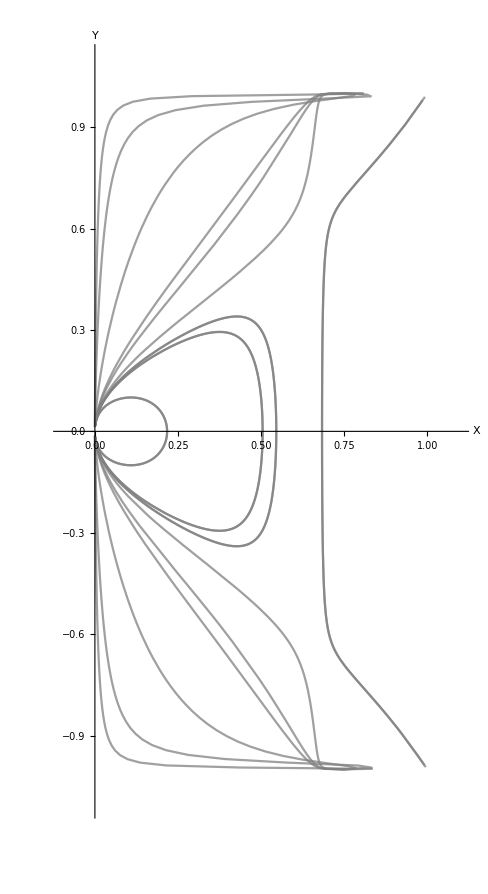

```mathematica
PhaseSpacexy=ParametricPlot[Evaluate[Table[{X1[t],Y1[t]}/.sol[i],{i,1,20}], {t,-80,80},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotRange->{{-0.1,1.1},{-1.1,1.1}},AxesLabel->{"X","Y"}]
```

```mathematica
PhaseSpaceFFS=ParametricPlot[Evaluate[Table[{X1[t],Y1[t]}/.sol[i],{i,21,22}], {t,-80,80},PlotStyle -> {{Darker[Green]}}],PlotRange->{{-0.1,1.1},{-1.1,1.1}},AxesLabel->{"X","Y"}];
```

InterpolatingFunction::dmval: Input value {-79.9967} lies outside the range of data in the interpolating function. Extrapolation will be used.

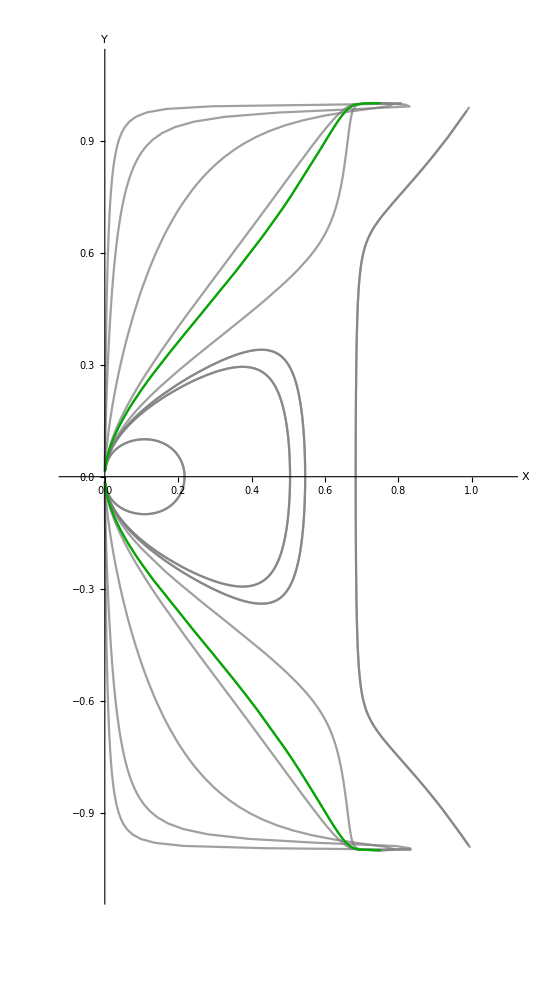

```mathematica
Show[PhaseSpacexy,PhaseSpaceFFS]
```

#### Fig 9 b 2

```mathematica
(*Clear all variables*)
ClearAll["Global`*"];
```

```mathematica
(*Define the dynamical system for compact interacting dark matter (Z) and dark energy (X)*)
deXt:=X1'[t]==-3*(Y1[t]/((1-Y1[t]^2)^(1/2)))*X1[t]*(1-X1[t])*(1+wx+ϵ*(X1[t]/(1-X1[t])))-q*X1[t]*(1-X1[t])*Z1[t]/(1-Z1[t])*(Y1[t]/((1-Y1[t]^2)^(1/2)))
deYt:=Y1'[t]==-Y1[t]^2*(1-Y1[t]^2)^(1/2)-(((1-Y1[t]^2)^(3/2))/6)*((X1[t]/(1-X1[t]))+(Z1[t]/(1-Z1[t]))+3*wx*(X1[t]/(1-X1[t]))+3*ϵ*(X1[t]^2/((1-X1[t])^2)))
deZt:=Z1'[t]==-3*Z1[t]*(1-Z1[t])*(Y1[t]/((1-Y1[t]^2)^(1/2))) + q*(X1[t]/(1-X1[t]))*Z1[t]*(1-Z1[t])*(Y1[t]/((1-Y1[t]^2)^(1/2)))
```

```mathematica
q=1;
wx=-0.5(*-0.390625*);
ϵ=-0.25;
```

```mathematica
(*Find x and y values at unstable spiral in this case*)
xSpiral=3/q/(1+3/q)
```

3/4

```mathematica
ySpiral=(√(-q wx-3 ϵ))/q/((1+((√(-q wx-3 ϵ))/q)^2)^(0.5))
```

0.745356

```mathematica
(*Plot the fixed points*)
FPShow=ListPlot[{{3/(3+q),-(√(-q wx-3 ϵ))/(√(q^2-q wx-3 ϵ))},{3/(3+q),(√(-q *wx-3 ϵ))/(√(q^2-q* wx-3 ϵ))}},PlotMarkers->{Automatic,Small},PlotStyle->{Black}];
```

```mathematica
traj[X0_,Y0_,Z0_]=NDSolve[{deXt,deYt,deZt, X1[0]==X0,Y1[0]==Y0,Z1[0]==Z0}, {X1,Y1,Z1},{t,-80,80}];
```

NDSolve::ndinnt: Initial condition X0 is not a number or a rectangular array of numbers.

```mathematica
sol[1]=traj[0.1,0.1,0.9];
sol[2]=traj[0.8,0.75,0.9];
sol[3]=traj[0.6,0.65,0.9];
sol[4]=traj[0.5,0.1,0.9];
sol[5]=traj[0.5,0.3,0.9];
sol[6]=traj[0.5,0.741,0.9]; 
sol[7]=traj[0.5,0.8,0.9];
sol[8]=traj[0.1,0.5,0.9];
sol[9]=traj[0.02,0.5,0.9];
sol[10]=traj[0.02,0.8,0.9];
```

```mathematica
sol[11]=traj[0.02,0.554,0.9]; 
sol[12]=traj[0.02,-0.554,0.9];
```

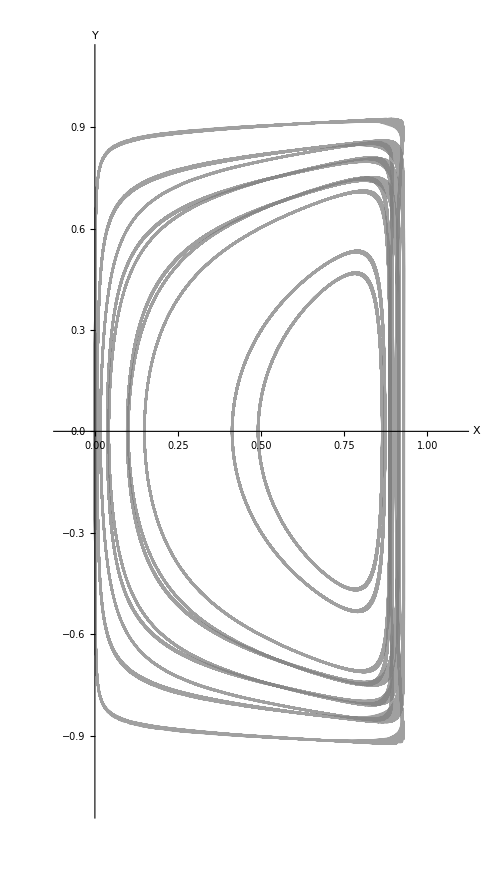

```mathematica
PhaseSpacexy=ParametricPlot[Evaluate[Table[{X1[t],Y1[t]}/.sol[i],{i,1,10}], {t,-80,80},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotRange->{{-0.1,1.1},{-1.1,1.1}},AxesLabel->{"X","Y"}]
```

```mathematica
PhaseSpaceFFS=ParametricPlot[Evaluate[Table[{X1[t],Y1[t]}/.sol[i],{i,11,12}], {t,-80,80},PlotStyle -> {{Darker[Green]}}],PlotRange->{{-0.1,1.1},{-1.1,1.1}},AxesLabel->{"X","Y"}];
```

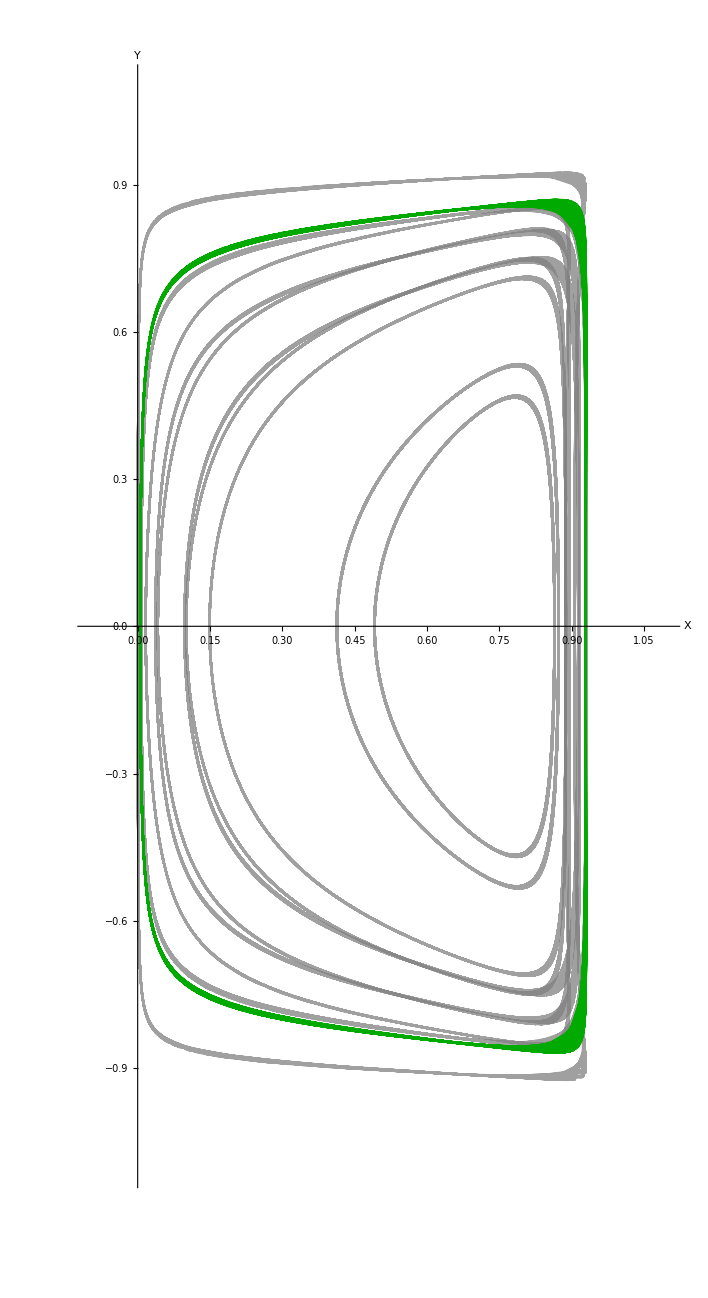

```mathematica
Show[PhaseSpacexy,PhaseSpaceFFS]
```

#### Test NDSolve

```mathematica
(*Dynamical system for a prey(x)-predator(y) system*)
de1:=x2'[t]==a*x2[t]-b*x2[t]*y2[t]
de2:=y2'[t]==-c*y2[t]+d*x2[t]*y2[t]
```

```mathematica
a=1;
b=1;
c=1;
d=1;
```

```mathematica
traj[x0_,y0_]=NDSolve[{de1,de2, x2[0]==x0,y2[0]==y0}, {x2,y2},{t,-80,80},AccuracyGoal->10,PrecisionGoal->10,MaxSteps->100000];
```

NDSolve::ndinnt: Initial condition x0 is not a number or a rectangular array of numbers.

```mathematica
sol[1]=traj[1,3];
sol[2]=traj[5,4];
sol[3]=traj[7,3];
sol[4]=traj[8,9];
```

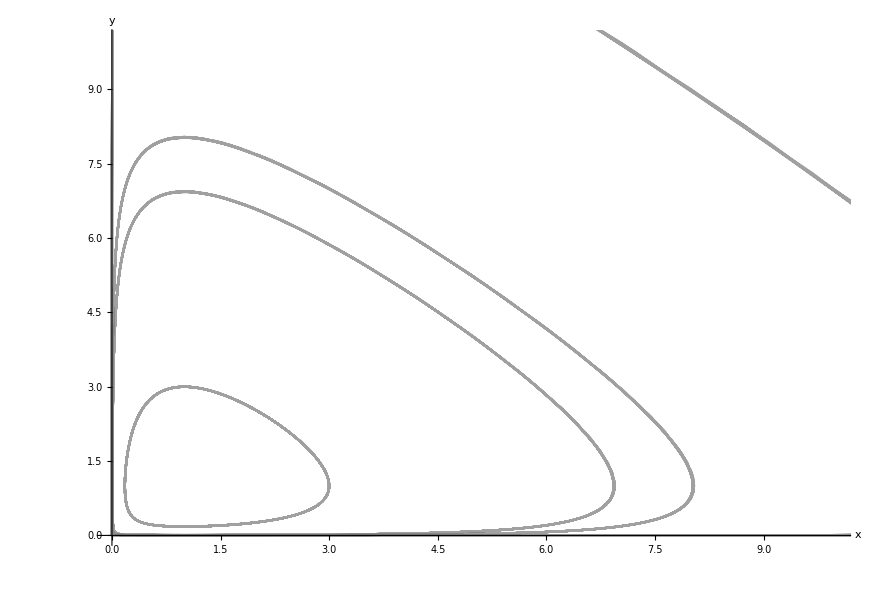

```mathematica
ParametricPlot[Evaluate[Table[{x2[t],y2[t]}/.sol[i],{i,1,4}], {t,-80,80},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotRange->{{0,10},{0,10}},AxesLabel->{"x","y"}]
```